```mathematica
Solve[P==1/3(ρ-4 B)+(4 λ^2)/(9 π^2)(-1+√(1+(3 π^2)/λ^2(ρ-B))),ρ]//Simplify//Expand
```

{{ρ→4 B+3 P+(4 λ^2)/π^2-(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2},{ρ→4 B+3 P+(4 λ^2)/π^2+(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2}}

```mathematica
Limit[4 B+3 P+(4 λ^2)/π^2-(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2,λ->0]
Limit[4 B+3 P+(4 λ^2)/π^2-(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2,λ->∞]

Limit[4 B+3 P+(4 λ^2)/π^2+(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2,λ->0]
Limit[4 B+3 P+(4 λ^2)/π^2+(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2,λ->∞]
```

4 B+3 P

2 B+P

4 B+3 P

∞

```mathematica
Simplify[(4 √(λ^2 (B π^2+P π^2+λ^2)))/π^2==(4 λ^2)/π^2 √(1+((P+B) π^2)/λ^2),λ>0]
```

True

```mathematica
Limit[4 B+3 P+(4 λ^2)/π^2(1-√(1+((P+B) π^2)/λ^2)),λ->0]
Limit[4 B+3 P+(4 λ^2)/π^2(1-√(1+((P+B) π^2)/λ^2)),λ->∞]

Limit[4 B+3 P+(4 λ^2)/π^2(1+√(1+((P+B) π^2)/λ^2)),λ->0]
Limit[4 B+3 P+(4 λ^2)/π^2(1+√(1+((P+B) π^2)/λ^2)),λ->∞]
```

4 B+3 P

2 B+P

4 B+3 P

∞

```mathematica
D[4 B+3 P+(4 λ^2)/π^2(1-√(1+((P+B) π^2)/λ^2)),P]
```

3-2/(√(1+((B+P) π^2)/λ^2))

```mathematica
1/(3-2/(√(1+((B+P) π^2)/λ^2)))/.{λ->√(4 B 10)}/.{B->145^4/197.327^3}
```

1/(3-2/(√(1+0.00428872 (57.5324+P))))

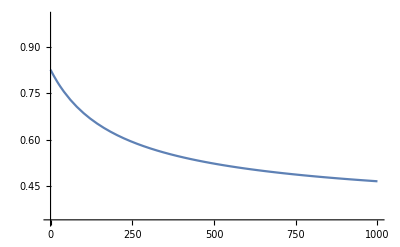

```mathematica
Plot[1/(3-2/(√(1+0.004288715968959339 (57.5323970654801+P)))),{P,0,1000},PlotRange->{1/3,1}]
```